```mathematica
D[Exp[-β((((x-n)^2)^-α+γ^-α)^(-1/α)+(((x-s)^2)^-α+γ^-α)^(-1/α)+(((x-e)^2)^-α+γ^-α)^(-1/α)+(((x-w)^2)^-α+γ^-α)^(-1/α)+θ(x-y)^2)],x]
```

-ⅇ^(-β ((((-e+x)^2)^-α+γ^-α)^(-1/α)+(((-n+x)^2)^-α+γ^-α)^(-1/α)+(((-s+x)^2)^-α+γ^-α)^(-1/α)+(((-w+x)^2)^-α+γ^-α)^(-1/α)+(x-y)^2 θ)) β (2 (-e+x) ((-e+x)^2)^(-1-α) (((-e+x)^2)^-α+γ^-α)^(-1-1/α)+2 (-n+x) ((-n+x)^2)^(-1-α) (((-n+x)^2)^-α+γ^-α)^(-1-1/α)+2 (-s+x) ((-s+x)^2)^(-1-α) (((-s+x)^2)^-α+γ^-α)^(-1-1/α)+2 (-w+x) ((-w+x)^2)^(-1-α) (((-w+x)^2)^-α+γ^-α)^(-1-1/α)+2 (x-y) θ)

```mathematica
FullSimplify[%]
```

-2 ⅇ^(-β ((((e-x)^2)^-α+γ^-α)^(-1/α)+(((n-x)^2)^-α+γ^-α)^(-1/α)+(((s-x)^2)^-α+γ^-α)^(-1/α)+(((w-x)^2)^-α+γ^-α)^(-1/α)+(x-y)^2 θ)) β ((((e-x)^2)^-α (((e-x)^2)^-α+γ^-α)^(-(1+α)/α))/(-e+x)+(((n-x)^2)^-α (((n-x)^2)^-α+γ^-α)^(-(1+α)/α))/(-n+x)+(((s-x)^2)^-α (((s-x)^2)^-α+γ^-α)^(-(1+α)/α))/(-s+x)+(((w-x)^2)^-α (((w-x)^2)^-α+γ^-α)^(-(1+α)/α))/(-w+x)+(x-y) θ)

```mathematica
Reduce[%==0 && 0≤x≤1,x]
```

$Aborted

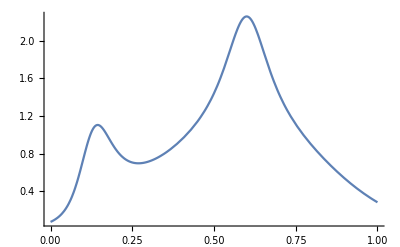

```mathematica
f[x_]:=Exp[-β(((((x-.134)^2)^-α+γ^-α)^(-1/α)+(((x-.12)^2)^-α+γ^-α)^(-1/α)+(((x-.112)^2)^-α+γ^-α)^(-1/α)+(((x-.6)^2)^-α+γ^-α)^(-1/α))/4+θ(x-.62)^2)]/.{γ->.01,α->1,θ->.03,β->300}
Plot[f[x]/NIntegrate[f[y],{y,0,1}],{x,0,1},PlotRange->All]
```

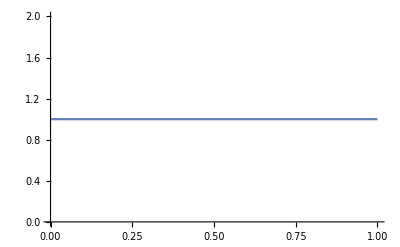

```mathematica
f[x_]:=Exp[-β(((((x-.134)^2)^-α+γ^-α)^(-1/α)+(((x-.144)^2)^-α+γ^-α)^(-1/α)+(((x-.112)^2)^-α+γ^-α)^(-1/α)+(((x-.124)^2)^-α+γ^-α)^(-1/α))/4+θ(x-.5)^2)]/.{γ->.01,α->1,θ->.03,β->0}
Plot[f[x]/NIntegrate[f[y],{y,0,1}],{x,0,1},PlotRange->All]
```

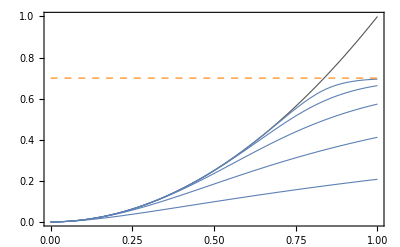

```mathematica
Show[
Plot[d^2,{d,0,1},PlotStyle->{GrayLevel[1/3],Thickness[.002]},PlotRange->{0,1},Frame->True],
Plot[((d^2)^-α+γ^-α)^(-1/α)/.{α->.5,γ->.7},{d,0,1},PlotRange->{0,1},PlotStyle->{Thickness[.002]}],
Plot[((d^2)^-α+γ^-α)^(-1/α)/.{α->1,γ->.7},{d,0,1},PlotRange->{0,1},PlotStyle->{Thickness[.002]}],
Plot[((d^2)^-α+γ^-α)^(-1/α)/.{α->2,γ->.7},{d,0,1},PlotRange->{0,1},PlotStyle->{Thickness[.002]}],
Plot[((d^2)^-α+γ^-α)^(-1/α)/.{α->4,γ->.7},{d,0,1},PlotRange->{0,1},PlotStyle->{Thickness[.002]}],
Plot[((d^2)^-α+γ^-α)^(-1/α)/.{α->8,γ->.7},{d,0,1},PlotRange->{0,1},PlotStyle->{Thickness[.002]}],
Plot[.7,{x,0,1},PlotStyle->{Thickness[.002],Dashed,Orange}]
]
```

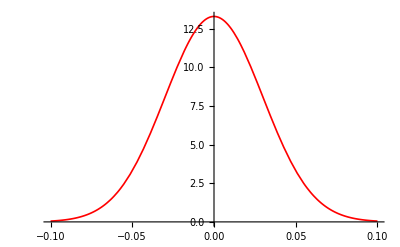

```mathematica
Plot[PDF[NormalDistribution[0,0.03],x],{x,-.1,.1},PlotStyle->{Red,Thickness[0.003]}]
```

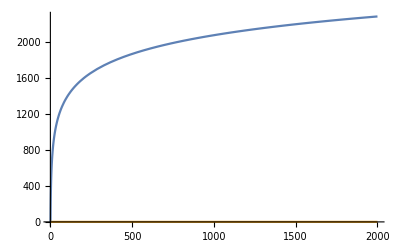

```mathematica
Plot[{300Log[n],1/512^2 Log[n]},{n,1,2000}]
```